# Quantum States

We will review the

## Key Concepts

Quantum Amplitudes

State Vector

Density Matrix

## State Vectors and Amplitudes

You have already seen bra-ket notation for quantum states like 0 or 1. The Dirac ket notation is in fact a shorthand representation of a vector, which is usually called state vector.

In the Wolfram quantum framework, it is “StateVector” property of a quantum state object

State vector of 0:

```mathematica
QuantumState["0"]["StateVector"]//Normal
```

{1,0}

State vector of 1:

```mathematica
QuantumState["1"]["StateVector"]//Normal
```

{0,1}

Now consider the result of applying a Hadamard gate to the register state:

```mathematica
state1=QuantumOperator["H"][]
```

QuantumState[…]

Return the corresponding state vector:

```mathematica
state1["StateVector"]//Normal
```

{1/(√2),1/(√2)}

Given the vector definitions for 0 and 1, the above vector can be rewritten as:

```mathematica
state1["Formula"]
```

1/(√2)0+1/(√2)1

In the representation above, 0and 1 serve as the basis of the complex vector space ℂ^2, and each term in the linear combination (the familiar quantum superposition) is the corresponding coefficient in that basis. For a single qubit, we write ψ=α0+β1, where α and β are complex amplitudes.

The coefficients of each basis element are known as the quantum amplitudes. A quantum state can be defined by giving its amplitudes:

```mathematica
QuantumState[{α,β}]["Amplitudes"]
```

<|0→α,1→β|>

This can be written in Dirac notation:

```mathematica
QuantumState[{α,β}]//TraditionalForm
```

α0+β1

Notice the relationship between the vector coefficients and the probabilities according to the Born’s rule:

```mathematica
QuantumState[{α,β}]["Probabilities"]
```

<|0→Abs[α]^2/(Abs[α]^2+Abs[β]^2),1→Abs[β]^2/(Abs[α]^2+Abs[β]^2)|>

Calculate probabilities for a quantum state:

```mathematica
QuantumState[{1,ⅈ √(3/4)}]["Probabilities"]
```

<|0→4/7,1→3/7|>

Calculate probabilities manually using state vector:

```mathematica
Abs[Normalize[{1,ⅈ √(3/4)}]]^2
```

{4/7,3/7}

Normalize the state vector directly:

```mathematica
QuantumState[Normalize@{1,ⅈ √(3/4)}]["StateVector"]//Normal
```

{2/(√7),ⅈ √(3/7)}

Use “Normalize” as the property of the quantum state object:

```mathematica
QuantumState[{1,ⅈ √(3/4)}]["Normalize"]["StateVector"]//Normal
```

{2/(√7),ⅈ √(3/7)}

However, there are situations where describing a qubit by a 2-vector is not enough. For example, in the famous Stern–Gerlach experiment—where a beam of silver atoms is sent through an inhomogeneous magnetic gradient—the initial state of the atoms, even if approximated by their electron spin only, may be an ensemble rather than a single pure state. In such cases, a state vector cannot fully describe the system. Instead, we use a density matrix (or density operator).

For instance, suppose a beam of silver atoms is prepared so that 30% are in0 and 70% are in 1. Mathematically, we describe this mixed state by the density matrix:

```mathematica
QuantumState[{{.3,0},{0,.7}}]
```

QuantumState[…]

Notice the tag “Mixed state” in the summary box of quantum state above.

Using “DensityMatrix” as the property, one can get the density matrix:

```mathematica
QuantumState[{{.3,0},{0,.7}}]["DensityMatrix"]//MatrixForm
```

(0.3 | 0
0 | 0.7)

An interesting feature of mixed states is that they lie inside the Bloch sphere, whereas pure states (those describable by a single 2-vector) lie only on the surface.

```mathematica
QuantumState[{{.3,0},{0,.7}}]["BlochPlot"]
```

-Graphics3D-

Computational-basis probabilities:

```mathematica
QuantumState[{{.3,0},{0,.7}}]["Probabilities"]
```

<|0→0.3,1→0.7|>

One can quantify if a state in pure or mixed. One measure is Tr[ρ^2], which will be one if pure state, while mixed states have Tr[ρ^2]<1. In the Wolfram quantum framework, “Purity” is a another property of a quantum state object:

```mathematica
QuantumState[{{.3,0},{0,.7}}]["Purity"]
```

0.58

Calculate purity for a pure state:

```mathematica
QuantumState[{.3,.7}]["Purity"]
```

1

### Example

Consider the quantum state 1/2 0+(√3)/2 1.

What is the state vector, the density matrix, the Bloch plot, and the measurement distribution in the computational basis?

##### Solution

Define the state with the given amplitudes:

```mathematica
state3=QuantumState[{1/2,√3/2}]
```

QuantumState[…]

Probabilities are the (normalized) norm squared of these amplitudes:

```mathematica
state3["Probabilities"]
```

<|0→1/4,1→3/4|>

Compute the state vector, density matrix, and Bloch plot:

```mathematica
state3["StateVector"]//MatrixForm//TraditionalForm
```

(1/2
(√3)/2)

```mathematica
state3["DensityMatrix"]//MatrixForm//TraditionalForm
```

(1/4 | (√3)/4
(√3)/4 | 3/4)

```mathematica
state3["BlochPlot"]
```

-Graphics3D-

The Bloch vector can be given in either spherical or Cartesian coordinates:

```mathematica
state3["BlochSphericalCoordinates"]
```

{1,(2 π)/3,0}

```mathematica
state3["BlochCartesianCoordinates"]
```

{(√3)/2,0,-1/2}

## Pauli Operators

You might have noticed that an X gate seems to act a lot like a NOT gate. That’s because they have identical effects on qubits. An X gate is a NOT gate.

```mathematica
QuantumOperator["X"]==QuantumOperator["NOT"]
```

True

Recall the Bloch sphere representation of a qubit:

```mathematica
GraphicsGrid[Apply[
QuantumState[#2]["BlochPlot",PlotLabel->Highlighted[QuantumState[QuantumState[#2],#1],Background->LightOrange]]&,{{{"Z","Up"},{"Z","Down"}},{{"X","+"},{"X","-"}},{{"Y","R"},{"Y","L"}}},{2}],Frame->All]
```

-Graphics-

Each of the six states shown above lie along the Cartesian axes of the sphere. For various historical reasons, these states have alternate names in the context of quantum computing. However, they have another interpretation in the context of linear algebra. They simply correspond to eigenvectors of the Pauli matrices:

```mathematica
Table[PauliMatrix[k]//MatrixForm,{k,3}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

```mathematica
Table[QuantumOperator[k]["Matrix"]//MatrixForm,{k,{"X","Y","Z"}}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

A future lesson will discuss the matrix representation of quantum states in more detail.

## States vs Measurements

While a measurement operation is always necessary to obtain practical results from quantum circuits, it is often helpful to analyze what happens to quantum states as each gate operation is applied to the qubits.

Consider the following quantum circuit:

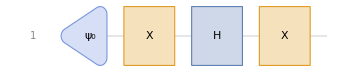

```mathematica
circuit1=QuantumCircuitOperator[{QuantumState[{1/2,√3/2},"Label"->Subscript[ψ,0]],"X","H","X"}];
circuit1["Diagram"]
```

What happens to the initial state after each gate is applied?

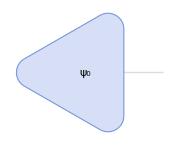
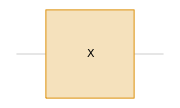
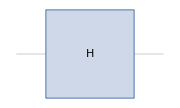
State 0 | State 1 | State 2 | State 3
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{states=ComposeList[circuit1["Operators"][[2;;]],circuit1["Operators"][[1]]["State"]]},
Grid[{Table[Style["State "<>ToString[n-1],"Text"],{n,Length[states]}],Map[#["BlochPlot",PlotLabel->Highlighted[#["FullSimplify"]["Formula"],Background->LightOrange]]&,states],Map[#["CircuitDiagram",ImageSize->Small,"WireLabels"->None]&,circuit1["Operators"]]},Alignment->Center,Frame->All,Spacings->{1,2}]
]
```

You can use the "AmplitudesPlot" property as another way of visualizing quantum states:

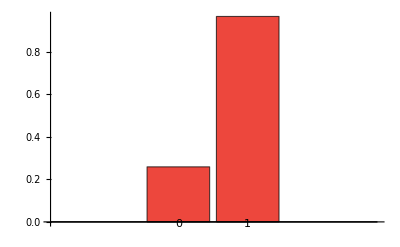

```mathematica
circuit1[]["AmplitudesPlot",ChartLegends->Automatic]
```

Recall that amplitudes do not have to be real numbers. They can take on complex values. What about a similar circuit but different initial state?

```mathematica
circuit2=QuantumCircuitOperator[{QuantumState[{1/2,ⅈ√3/2}],"X","H","X"}]
```

QuantumCircuitOperator[…]

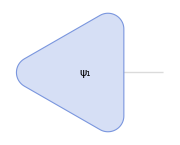
State 0 | State 1 | State 2 | State 3
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{circuit=circuit2,states},
states=ComposeList[circuit["Operators"][[2;;]],circuit["Operators"][[1]]["State"]];
Grid[{Table[Style["State "<>ToString[n-1],"Text"],{n,Length[states]}],Map[#["BlochPlot",PlotLabel->Highlighted[#["Simplify"]["Formula"],Background->LightOrange]]&,states],Map[#["CircuitDiagram",ImageSize->Small,"WireLabels"->None]&,circuit["Operators"]]},Alignment->Center,Frame->All,Spacings->{1,2}]
]
```

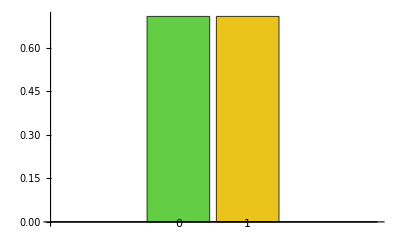

```mathematica
circuit2[]["Simplify"]["AmplitudesPlot",ChartLegends->Automatic]
```

Even though the measurement distributions for each of the two initial states were identical, they are different quantum states. Thus, this circuit has very different effects on them.

```mathematica
circuit1[]==circuit2[]
```

False

```mathematica
QuantumState[{1/2,√3/2}]["Probabilities"]
```

<|0→1/4,1→3/4|>

```mathematica
QuantumState[{1/2,ⅈ√3/2}]["Probabilities"]
```

<|0→1/4,1→3/4|>

Constructing a quantum state based solely on measured outcome probabilities is a complicated process, usually referred to as quantum state tomography. This procedure typically requires measurements in multiple bases and careful statistical reconstruction, and it is beyond the scope of our introductory course. For more details, you can read our documentation page on QuantumStateEstimate.

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]